```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["nonscattering_branch.wl"]
```

Continuation to eps = 0.05 with N = 24, M = 256:

eps = 0.00500   k = 2.23091941   kappa = 5.13584059   sigma = 5.29974904   max|F| = 1.6e-14

eps = 0.01000   k = 2.23111297   kappa = 5.13649898   sigma = 5.30018818   max|F| = 3.1e-14

eps = 0.01500   k = 2.23144235   kappa = 5.13760848   sigma = 5.30091288   max|F| = 4.1e-14

eps = 0.02000   k = 2.23191849   kappa = 5.13918887   sigma = 5.30191178   max|F| = 2.1e-14

eps = 0.02500   k = 2.23255847   kappa = 5.14127126   sigma = 5.30316761   max|F| = 1.2e-14

eps = 0.03000   k = 2.23338801   kappa = 5.14390299   sigma = 5.30465540   max|F| = 1.4e-14

eps = 0.03500   k = 2.23444644   kappa = 5.14715736   sigma = 5.30633901   max|F| = 2.6e-14

eps = 0.04000   k = 2.23579760   kappa = 5.15115530   sigma = 5.30816379   max|F| = 2.8e-14

eps = 0.04500   k = 2.23756085   kappa = 5.15612718   sigma = 5.31003683   max|F| = 5.6e-14

eps = 0.05000   k = 2.24008186   kappa = 5.16275683   sigma = 5.31172472   max|F| = 3.1e-14

Resonant disk (seed), cf. (1.13):

k_* = 2.230855550630   kappa_* = j_(2,1) = 5.135622301841   sigma_* = 5.299601954813

Domain at eps = 0.05:

k = 2.2400818639   kappa = 5.1627568292   sigma = 5.3117247221

rho(0) = 1.069167 (long axis)   rho(pi/2) = 0.956943 (short axis)

curvature: min = 0.8656, max = 2.6053   (convex)

min of J_0(k rho) on the boundary = 0.00510

leading coefficients a_2, a_3, a_4 = 9.4e-3, 3.7e-3, 1.9e-3

size of last retained coefficient |a_N| = 2.1e-5   (should be negligible)

Check against Proposition 1.4, at eps = 0.005:

a_2 / eps^2               = 2.95225   predicted by (1.15): 3/4 + kappa_*^2/12 = 2.94788

[sigma - sigma_*] / eps^2   = 5.88331   predicted by (1.16): c_*                = 5.89028

Written:

nonscattering_branch.csv

```mathematica
br004=branch[[8]]
```

{0.04,0.00531557,0.00140793,0.000478836,0.000184435,0.0000765532,0.0000334022,0.0000151045,7.01607×10^-6,3.32779×10^-6,1.60503×10^-6,7.84797×10^-7,3.8814×10^-7,1.93828×10^-7,9.75976×10^-8,4.94971×10^-8,2.52608×10^-8,1.29635×10^-8,6.68545×10^-9,3.46295×10^-9,1.80004×10^-9,9.44864×10^-10,4.56635×10^-10,3.69885×10^-10,2.2358,5.15116}

```mathematica
bdry004[t_]:=1+br004[[1]]Cos[2t]+Sum[br004[[j]]Cos[2j t],{j,2,24}];
ell[a_,b_,t_]:=a b/Sqrt[b^2Cos[t]^2+a^2Sin[t]^2];
Ω=ParametricRegion[r bdry004[t] {Cos[t], Sin[t]},{{r,0,1}, {t,0,2Pi}}];
```

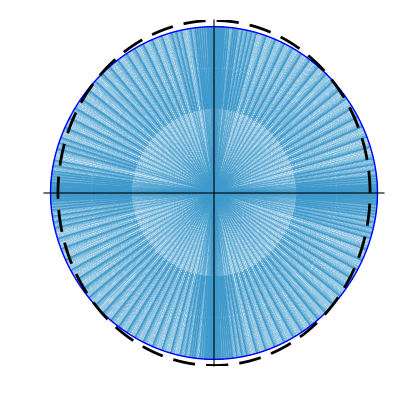

```mathematica
fignew1=Show[RegionPlot[Ω, BoundaryStyle->Directive[Blue,Thick]], ParametricPlot[{Cos[t],Sin[t]}, {t,0,2Pi}, PlotStyle->{Dashing[{0.04,0.02}],Black}],Axes->True,Frame->False, Ticks->None,AspectRatio->1]
```

{0.0000597421,{a→1.04151,b→0.960921}}

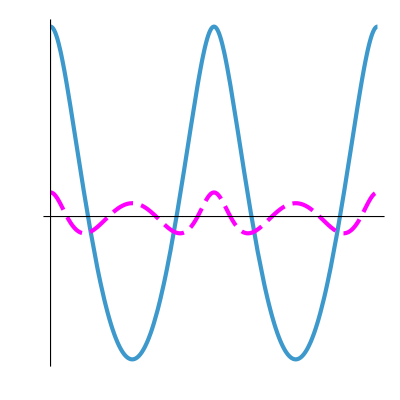

```mathematica
optellipse[a_?NumericQ,b_?NumericQ]:=NIntegrate[(bdry004[t]-ell[a,b,t])^2,{t,0,2 Pi},Method->{"Trapezoidal","SymbolicProcessing"->0}];
min=FindMinimum[optellipse[a,b],{{a,1.04},{b,0.96}}]
fignew2=Plot[{bdry004[t]-1,bdry004[t]-ell[a,b,t]/.min[[2]]}, {t,0,2Pi},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[3],Dashing[{0.04,0.015}], Magenta}}, Ticks->{{{Pi/2, MaTeX["\\frac{\\pi}{2}"]}, {Pi, MaTeX["\\pi"]},{3Pi/2, MaTeX["\\frac{3\\pi}{2}"]},{2 Pi, MaTeX["2\\pi"]}},Table[{y, MaTeX[y]}, {y,{-0.04,-0.02,0.02,0.04}}]},AxesLabel->{MaTeX["\\theta"],None},AspectRatio->1]
```

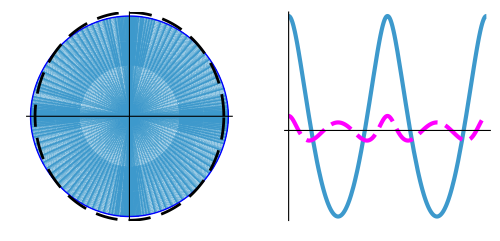

```mathematica
fignew=GraphicsRow[{fignew1, fignew2},ImageSize->500]
```

```mathematica
Export["fignew.pdf", fignew]
```